## Input shaping (robust version) (Problem 9.1)

```mathematica
Clear["Global`*"];
```

ZV shaper  (zero vibration)

```mathematica
v1=√((A1+A2 Cos[ ω τ])^2+(A2 Sin[ω τ])^2)//Simplify
```

√(A1^2+A2^2+2 A1 A2 Cos[τ ω])

```mathematica
v1/.{A2->A1,τ->π}//Simplify
```

2 √(A1^2 Cos[(π ω)/2]^2)

```mathematica
v1a=v1/.{A1->1/2,A2->1/2,τ->π}
```

√(1/2+1/2 Cos[π ω])

```mathematica
v1s=Abs[Series[v1a,{ω,1,1}]]//Normal; TraditionalForm[v1s]
```

(π Abs[ω-1])/2

ZVD shaper (zero vibration + zero derivative wrt ω), for robustness

```mathematica
v2=√((A1+A2 Cos[π ω]+A3 Cos[2π ω])^2+(A2 Sin[π ω]+A3 Sin[2π ω])^2)//Simplify
```

√((A1+A2 Cos[π ω]+A3 Cos[2 π ω])^2+(A2 Sin[π ω]+A3 Sin[2 π ω])^2)

```mathematica
v2a=v2/.{A3->A1,A2->1-2A1}//Simplify
```

√((1-2 A1+2 A1 Cos[π ω])^2)

```mathematica
dv2dω=D[v2a^2,ω]//Simplify;  TraditionalForm[dv2dω]
```

-4 π A1 sin(π ω) (2 A1 cos(π ω)-2 A1+1)

```mathematica
v2a = v2/.{A1->1/4,A2->1/2,A3->1/4};  v2as=Simplify[v2a,ω>0]
```

Cos[(π ω)/2]^2

```mathematica
v2/.{A3->A1,A2->1-2A1}//FullSimplify
```

√((1-2 A1+2 A1 Cos[π ω])^2)

```mathematica
v2s=Series[v2as,{ω,1,2}]//Normal;   TraditionalForm[v2s]
```

1/4 π^2 (ω-1)^2

ZVDD shaper (zero vibe + zero 1st and 2nd derivatives wrt ω)

```mathematica
v4=√((A1+A2 Cos[π ω]+A3 Cos[2π ω]+A4 Cos[3π ω])^2+(A2 Sin[π ω]+A3 Sin[2π ω]+A4 Sin[3π ω])^2)/.{A4->A1,A3->A2}//Simplify
```

2 √(Cos[(π ω)/2]^2 (-A1+A2+2 A1 Cos[π ω])^2)

```mathematica
v4d = D[v4^2,ω]//Simplify
```

-2 π (-A1+A2+2 A1 Cos[π ω]) (3 A1+A2+6 A1 Cos[π ω]) Sin[π ω]

```mathematica
v4dd=D[v4d,ω]//Simplify
```

-2 π^2 (A2 (2 A1+A2) Cos[π ω]+A1 (8 A2 Cos[2 π ω]+9 A1 Cos[3 π ω]))

```mathematica
v4dd1=v4dd/.ω->1
```

-2 (-A2 (2 A1+A2)+A1 (-9 A1+8 A2)) π^2

```mathematica
Solve[v4dd1==0,A1]
```

{{A1→A2/3},{A1→A2/3}}

```mathematica
v4s=Abs[Series[v4/.{A1->1/8,A2->3/8},{ω,1,4}]//Normal];   TraditionalForm[v4s]
```

1/8 π^3 Abs[ω-1]^3

```mathematica
Simplify[v4/.{A1->1/8,A2->3/8},ω>0]
```

Abs[Cos[(π ω)/2]]^3

Graphical summary of residual amplitudes as a function of frequency about ω=1

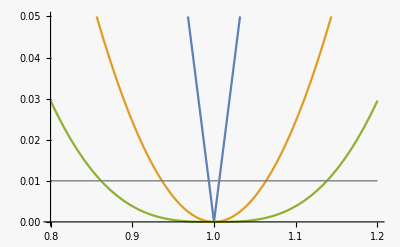

```mathematica
Plot[{v1/.{A1->1/2,A2->1/2,τ->π},v2/.{A1->1/4,A2->1/2,A3->1/4},v4/.{A1->1/8,A2->3/8},0.01},{ω,0.8,1.2},PlotRange->{0,0.05},PlotStyle->{,,,Directive[Gray,Thin]}]
```

A note on statistics:  assume that ω is a Gaussian random variable with mean 1 and variance σ^2
can transpose to δω, which is Gaussian about 0.  Need moments:

```mathematica
Expectation[{(π/2)Abs[x],(π/2)^2 x^2,(π/2)^3 x^2 Abs[x]},x\[Distributed]NormalDistribution[0,σ]]
```

{√(π/2) σ,(π^2 σ^2)/4,(π^(5/2) σ^3)/(2 √2)}

Simulate dynamics assuming ω=1 but actually ω=1.15 using naive, ZV, ZVD, and ZVDD

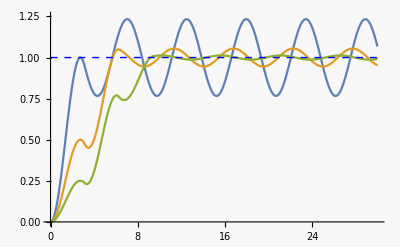

```mathematica
tmax=30;
Gtf=TransferFunctionModel[1/(1+(s/ω0)^2)/.ω0->1.15,s];
uNaive = UnitStep[t];

yNaive=OutputResponse[Gtf,uNaive,{t,0,tmax}];
uZV=1/2(UnitStep[t]+UnitStep[t-π]);
yZV=OutputResponse[Gtf,uZV,{t,0,tmax}];
uZVD=1/4(UnitStep[t]+2UnitStep[t-π]+UnitStep[t-2π]);
yZVD=OutputResponse[Gtf,uZVD,{t,0,tmax}];
uZVDD=1/8(UnitStep[t]+3(UnitStep[t-π]+UnitStep[t-2π])+UnitStep[t-3π]);
yZVDD=OutputResponse[Gtf,uZVDD,{t,0,tmax}];
Plot[{yZV,yZVD,yZVDD,1},{t,0,tmax},PlotRange->{0,1.25},PlotStyle->{,,,Directive[Blue,Dashed,Thin]}]
```

Export data

```mathematica
dat= Table[{yZV[[1]],yZVD[[1]],yZVDD[[1]]},{t,0,tmax,0.01}];
```

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["inputShaping.dat", dat];
*)
```

Simulate dynamics assuming ω=1 but actually ω=1.15 using adiabatic ramp

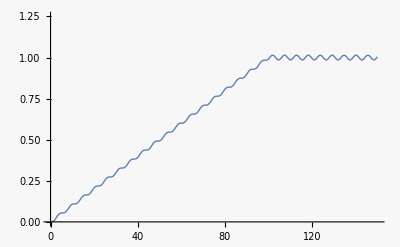

```mathematica
tad=100;uad=Piecewise[{{t/tad,t<tad},{1,t≥ tad}}];
yad = OutputResponse[Gtf,uad,{t,0,1.5tad}];
Plot[yad,{t,0,1.5tad},PlotRange->{0,1.25}]
```

```mathematica
uad0=Piecewise[{{t/Tr,t<Tr},{1,t≥ Tr}}]
ysol=DSolveValue[{y''[t]+ω^2 y[t]==ω^2 t/Tr,y[0]==0,y'[0]==0},y[t],t,Assumptions-> {Tr>0,ω>0}]//Simplify
```

Piecewise[{{t/Tr, t<Tr}, {1, t≥Tr}, {0, True}}]

(t ω-Sin[t ω])/(Tr ω)

```mathematica
D[ysol,t]//Simplify
```

(1-Cos[t ω])/Tr

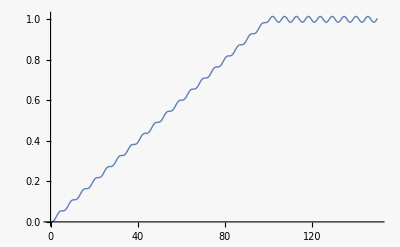

```mathematica
Plot[(t ω-Sin[t ω]+((-t+Tr) ω+Sin[(t-Tr) ω]) UnitStep[t-Tr])/(Tr ω)/.{ω->1.15,Tr->100},{t,0,150}]
```

```mathematica
(Sin[θ]/θ)^2+ ((1-Cos[θ])/θ)^2//Expand//FullSimplify
```

(2-2 Cos[θ])/θ^2

EVD shaper kills two frequencies, for robustness.  Method:  keep τ and 2τ same; keep A1=A3 by symmetry;  use additional freedom to set V(ω=1) = 0.05.
[omit:  this is lousy if expected value of ω has no bias!]

```mathematica
v3=Sqrt[(A1+A2 Cos[ω τ]+A3 Cos[2ω τ])^2+(A2 Sin[ω τ]+A3 Sin[2ω τ])^2];
v3a=v3/.{A3->A1,A2->1-2A1}//Simplify
```

√((1-2 A1+2 A1 Cos[τ ω])^2)

```mathematica
v3b=Simplify[v3a/.{τ->π,ω->1},A1>0]
```

Abs[1-4 A1]

```mathematica
(1+0.05)/4//N    (* solve for A1 *)
```

0.2625

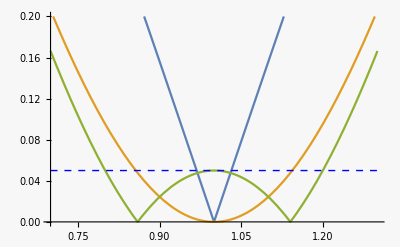

```mathematica
Plot[{v1/.{A1->1/2,A2->1/2,τ->π},v2/.{A1->1/4,A2->1/2,A3->1/4},v3a/.{A1->0.2625,τ->π},0.05},{ω,0.7,1.3},PlotRange->{0,0.2},PlotStyle->{,,,Directive[Blue,Dashed,Thin]}]
```

Robust minmax solution for two impulses

```mathematica
j=(a0+a1 Cos[ω t1]+a2 Cos[ω t2])^2+(a1 Sin[ω t1]+a2 Sin[ω t2])^2/.{a2->a0,a1->1-2a0,t2->2 t1}//FullSimplify
```

(1-2 a0+2 a0 Cos[t1 ω])^2

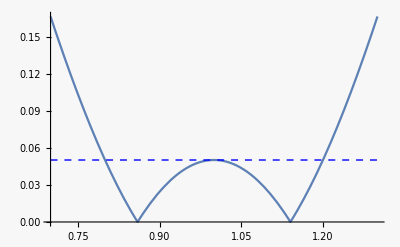

```mathematica
j1=Abs[1-2 a0+2 a0 Cos[t1 ω]]; j1max=j1//.{a0->1/(2(1+Cos[π/2 ϵ]^2)),t1->π,ϵ->0.2,ω->1};
Plot[{j1//.{a0->1/(2(1+Cos[π/2 ϵ]^2)),t1->π,ϵ->0.2},j1max},{ω,0.7,1.3},PlotStyle->{,Directive[Blue,Dashed,Thin]}]
```

```mathematica
{j1//.{a0->1/(2(1+Cos[π/2 ϵ]^2)),t1->π,ϵ->0.2,ω->1},j1//.{a0->1/(2(1+Cos[π/2 ϵ]^2)),t1->π,ϵ->0.2,ω->1-ϵ},j1//.{a0->1/(2(1+Cos[π/2 ϵ]^2)),t1->π,ϵ->0.2,ω->1+ϵ}}
```

{0.0501397,0.0501397,0.0501397}

The three values are equal.  (They are at the intersection of the horizontal dashed line above with the curve.)